### Start choosing the example:

```mathematica
t=23;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]/.{I1->312/100, U1->2,S1->0,S2->0};
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.314398,Null}

<|j955→78/25,u983→2,j951→78/25+0-52/25+0,j952→78/25+0-52/25+0,j954→78/25,j956→0,j957→0,j959→0,j960→0,jt962→0,jt963→0,jt964→0,jt965→78/25-52/25+0,jt966→52/25-0,jt967→78/25+0-52/25+0,jt968→0,jt969→0,jt970→78/25-52/25+0,jt971→0,jt972→52/25-0,jt973→0,jt974→0,u978→2,u980→-78/25-0+52/25+102/25,u981→-78/25-0+52/25+76/25,u982→-0+52/25+2,u984→102/25,j953→0,j958→52/25,jt961→0,u975→102/25,u976→76/25,u977→2,u979→102/25|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{26/25,26/25,0,78/25,78/25,0,0,52/25,0,0,0,0,0,0,26/25,52/25,26/25,0,0,26/25,0,52/25,0,0,102/25,76/25,2,2,102/25,76/25,2,102/25,2,102/25}

{26/25,26/25,0,78/25,78/25,0,0,52/25,0,0,0,0,0,0,26/25,52/25,26/25,0,0,26/25,0,52/25,0,0,102/25,76/25,2,2,102/25,76/25,2,102/25,2,102/25}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{j952,78/25,78/25,j957,78/25-j952+j953+j957,0,0,j957,0,j953,0,j952-j953,78/25-j952+j953,j952,j957,j953,j952-j953,j957,78/25-j952+j953,0,0,u979,2,2,u976,2,u979,2,u979}

{j952,78/25,78/25,j957,78/25-j952+j953+j957,0,0,j957,0,j953,0,j952-j953,78/25-j952+j953,j952,j957,j953,j952-j953,j957,78/25-j952+j953,0,0,u979,2,2,u976,2,u979,2,u979}

#### Non-linear case with alpha != 1

```mathematica
Parameters["alpha"]=.8;
Parameters
```

<|alpha→0.8,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1084794[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1084794[x$]-g$1084794[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

$Aborted

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0570273&&j952-j957-u976+u981==-0.0570273&&j953-j958-u977+u982==-0.172976

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0586421&&j952-j957-u976+u981==-0.0586421&&j953-j958-u977+u982==-0.176256

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0588982&&j952-j957-u976+u981==-0.0588982&&j953-j958-u977+u982==-0.176783

0.000639752

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0570273&&j952-j957-u976+u981==-0.0570273&&j953-j958-u977+u982==-0.172976

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0586421&&j952-j957-u976+u981==-0.0586421&&j953-j958-u977+u982==-0.176256

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0588982&&j952-j957-u976+u981==-0.0588982&&j953-j958-u977+u982==-0.176783

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0589391&&j952-j957-u976+u981==-0.0589391&&j953-j958-u977+u982==-0.176868

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==-0.0589456&&j952-j957-u976+u981==-0.0589456&&j953-j958-u977+u982==-0.176881

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j951-j956-u975+u980==3.12+1. j953-1. j958+Intg[3.12+1. j953-1. j958]&&j952-j957-u976+u981==3.12+1. j953-1. j958+Intg[3.12+1. j953-1. j958]&&j953-j958-u977+u982==j953-j958+Intg[j953-j958]

√(Abs[-0.176881-1. j953+1. j958-Intg[j953-j958]]^2+2 Abs[-3.17895-1. j953+1. j958-Intg[3.12+1. j953-1. j958]]^2)

```mathematica
sol36It=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: j951-j956-u975+u980==-0.0570273&&j952-j957-u976+u981==-0.0570273&&j953-j958-u977+u982==-0.172976

FixedX3: next step: j951-j956-u975+u980==-0.0586421&&j952-j957-u976+u981==-0.0586421&&j953-j958-u977+u982==-0.176256

FixedX3: next step: j951-j956-u975+u980==-0.0588982&&j952-j957-u976+u981==-0.0588982&&j953-j958-u977+u982==-0.176783

FixedX3: next step: j951-j956-u975+u980==-0.0589391&&j952-j957-u976+u981==-0.0589391&&j953-j958-u977+u982==-0.176868

FixedX3: next step: j951-j956-u975+u980==-0.0589456&&j952-j957-u976+u981==-0.0589456&&j953-j958-u977+u982==-0.176881

The system is False. Returning the inputs.

FixedX3: next step: j951-j956-u975+u980==3.12+1. j953-1. j958+Intg[3.12+1. j953-1. j958]&&j952-j957-u976+u981==3.12+1. j953-1. j958+Intg[3.12+1. j953-1. j958]&&j953-j958-u977+u982==j953-j958+Intg[j953-j958]

Throw::nocatch: Uncaught Throw[<|j955→3.12,u983→2,j951→3.12+1. 0-1. 2.17825+1. 0,«28»,u976→3.00069,u977→2.,u979→4.00138|>] returned to top level.

Hold[Throw[<|j955→3.12,u983→2,j951→3.12+1. 0-1. 2.17825+1. 0,j952→3.12+1. 0-1. 2.17825+1. 0,j954→3.12,j956→0.+1. 0,j957→0.+1. 0,j959→0.,j960→0.,jt962→0.,jt963→0.+1. 0,jt964→0.,jt965→3.12-1. 2.17825+1. 0,jt966→0.+1. 2.17825-1. 0,jt967→3.12+1. 0-1. 2.17825+1. 0,jt968→0.+1. 0,jt969→0.+1. 0,jt970→3.12-1. 2.17825+1. 0,jt971→0.+1. 0,jt972→0.+1. 2.17825-1. 0,jt973→0.,jt974→0.,u978→2,u980→-3.17894-1. 0+1. 2.17825+1. 4.00138,u981→-3.17894-1. 0+1. 2.17825+1. 3.00069,u982→-0.176868-1. 0+1. 2.17825+1. 2.,u984→4.00138,j953→0,j958→2.17825,jt961→0,u975→4.00138,u976→3.00069,u977→2.,u979→4.00138|>]]

ReplaceAll::reps: {Hold[Throw[<|j955→3.12,u983→2,j951→3.12+1. 0-1. 2.17825+1. 0,«28»,u976→3.00069,u977→2.,u979→4.00138|>]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1084794[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1084794[x$]-g$1084794[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j955→78/25,u983→2,j951→78/25+0-52/25+0,j954→78/25,j956→0,j958→52/25,j959→0,j960→0,jt961→0,jt962→0,jt963→0,jt964→0,jt965→78/25-52/25+0,jt966→52/25-0,jt967→78/25+0-52/25+0,jt968→0,jt969→0,jt970→78/25-52/25+0,jt971→0,jt972→52/25-0,jt973→0,jt974→0,u978→2,u984→102/25,u975→102/25,u977→2,u980→-78/25-0+52/25+102/25,u981→-78/25-0+52/25+76/25,u982→-0+52/25+2,j952→78/25+0-52/25+0,j957→0,j953→0,u976→76/25,u979→102/25|>

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j951-j956-u975+u980==0&&j952-j957-u976+u981==0&&j953-j958-u977+u982==0

<|j955→78/25,u983→2,j951→78/25+0-52/25+0,j952→78/25+0-52/25+0,j954→78/25,j956→0,j957→0,j959→0,j960→0,jt962→0,jt963→0,jt964→0,jt965→78/25-52/25+0,jt966→52/25-0,jt967→78/25+0-52/25+0,jt968→0,jt969→0,jt970→78/25-52/25+0,jt971→0,jt972→52/25-0,jt973→0,jt974→0,u978→2,u980→-78/25-0+52/25+102/25,u981→-78/25-0+52/25+76/25,u982→-0+52/25+2,u984→102/25,j953→0,j958→52/25,jt961→0,u975→102/25,u976→76/25,u977→2,u979→102/25|>

```mathematica
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.nsol2]//Chop
```

0

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]
```

FixedX3: next step: j951-j956-u975+u980==0&&j952-j957-u976+u981==0&&j953-j958-u977+u982==0

<|j955→78/25,u983→2,j951→78/25+0-52/25+0,j952→78/25+0-52/25+0,j954→78/25,j956→0,j957→0,j959→0,j960→0,jt962→0,jt963→0,jt964→0,jt965→78/25-52/25+0,jt966→52/25-0,jt967→78/25+0-52/25+0,jt968→0,jt969→0,jt970→78/25-52/25+0,jt971→0,jt972→52/25-0,jt973→0,jt974→0,u978→2,u980→-78/25-0+52/25+102/25,u981→-78/25-0+52/25+76/25,u982→-0+52/25+2,u984→102/25,j953→0,j958→52/25,jt961→0,u975→102/25,u976→76/25,u977→2,u979→102/25|>

### What is this plot for?

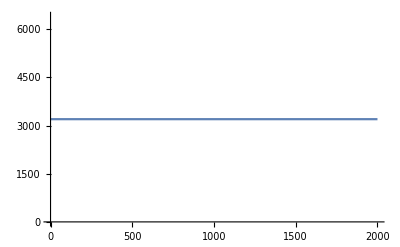
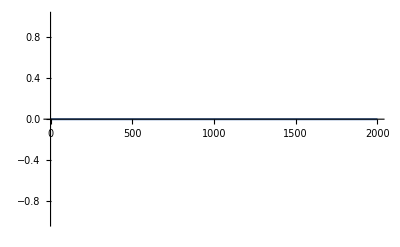
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.